# HyperBloch package tutorial

## Haldane model; point-group matrices

This notebook provides solved exercises aimed to introduce the functionality of the  HyperBloch package for efficient modeling of tight-binding models on hyperbolic lattices. It is intended to be used in tandem with the HyperBloch Haldane model tutorial on the HyperCells&HyperBloch website.  In this tutorial, we will see an example of how symmetry analysis of next-nearest-neighbor tessellation (supercell) model graphs can be conducted. In particular, point-group matrices (constructed through HyperBloch’s sister package HyperCells) are imported and used to perform a symmetry transformation for a variant of the Haldane model on a hyperbolic lattice, where we will see how corresponding spectra are effected.

## Preliminaries:

### Remarks:

Before using the notebook to the Haldane model tutorial:

Make sure that the HyperBloch package is installed, if this is not the case please follow the instruction on the website HyperCells&HyperBloch installation.

Make sure that the required files .hcc,  .hcm and .hcs files are in the current directory. This entails files:

(2,4,6)_T2.2_3.hcc
{6,4}-tess-NNN_T2.2_3.hcm
{6,4}-tess-NNN_T2.2_3_sc-T5.4.hcs
{6,4}-tess-NNN_T2.2_3_sc-T9.3.hcs

In case no such files exist in your current directory, please follow the instructions in the  HyperBloch Haldane model tutorial, or download the files there.

### Documentation:

You may want to take a look at the basic usage guide of the HyperBloch package or the available functions within the package, respectively:

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/tutorial/BasicUsage"];
```

```mathematica
Documentation`HelpLookup["PatrickMLenggenhager/HyperBloch/guide/HyperBlochPackage"];
```

### Load the HyperBloch package:

The HyperBloch package can be loaded as follows:

```mathematica
<<PatrickMLenggenhager`HyperBloch`
```

Set the directory of the needed HyperCells files remarked above, which is assumed to be the directory of this file:

```mathematica
SetDirectory[NotebookDirectory[]];
```

## (Supercell) model graphs:

### Preliminaries:

We consider the following sequence of supercells, defined in terms of triangle group quotients given in the tabulated list of quotients by Marston Conder:

```mathematica
cells={"T2.2","T5.4","T9.3"};
```

where we consider the unit cell T2.2 as the primitive cell.

### Import (supercell) model graphs:

We first import the cell, model, and supercell model graphs as produced by the HyperCells package:

Cell graph:

```mathematica
pcell=ImportCellGraphString[Import["(2,4,6)_T2.2_3.hcc"]];
```

Primitive cell:

```mathematica
pcmodel=ImportModelGraphString[Import["{6,4}-tess-NNN_T2.2_3.hcm"]];
```

Consecutive supercells:

```mathematica
scmodels=Association[#->ImportSupercellModelGraphString[ Import["{6,4}-tess-NNN_T2.2_3_sc-"<>#<>".hcs"]]&/@cells[[2;;]]];
```

We can extract the genera of the compactified unit cells programmatically:

```mathematica
genusLst= Join[
Association[cells[[1]]->pcmodel["Genus"]],
Association[#->scmodels[#]["Genus"]&/@cells[[2;;]]]
];
```

### Visualize the primitive cell:

Let us visualize the NN and NNN-terms of the graph representation for the next-nearest-neighbor tight-binding model on the primitive cell. They are stored as directed edges, which can be extracted from the model graph as follows:

```mathematica
EdgeList@pcmodel["Graph"]
```

{{2,1}{2,2}{1,{{1,1},1,7}},{2,3}{2,1}{1,{{1,2},6,12}},{2,1}{2,3}{1,{{1,3},13,23}},{2,2}{2,4}{1,{{1,4},2,8}},{2,4}{2,2}{1,{{1,5},15,19}},{2,2}{2,1}{1,{{1,6},14,24}},{2,5}{2,3}{1,{{1,7},5,11}},{2,3}{2,5}{1,{{1,8},18,22}},{2,4}{2,6}{1,{{1,9},3,9}},{2,6}{2,4}{1,{{1,10},16,20}},{2,6}{2,5}{1,{{1,11},4,10}},{2,5}{2,6}{1,{{1,12},17,21}},{2,1}{2,4}{2,{1,1,4}},{2,2}{2,6}{2,{1,4,9}},{2,4}{2,5}{2,{1,9,11}},{2,6}{2,3}{2,{1,11,7}},{2,5}{2,1}{2,{1,7,2}},{2,3}{2,2}{2,{1,2,1}},{2,2}{2,3}{2,{2,1,3}},{2,1}{2,5}{2,{2,3,7}},{2,3}{2,6}{2,{2,7,12}},{2,5}{2,4}{2,{2,12,9}},{2,6}{2,2}{2,{2,9,5}},{2,4}{2,1}{2,{2,5,1}},{2,4}{2,1}{2,{3,4,6}},{2,2}{2,3}{2,{3,6,2}},{2,1}{2,5}{2,{3,2,8}},{2,3}{2,6}{2,{3,8,11}},{2,5}{2,4}{2,{3,11,10}},{2,6}{2,2}{2,{3,10,4}},{2,2}{2,6}{2,{4,5,10}},{2,4}{2,5}{2,{4,10,12}},{2,6}{2,3}{2,{4,12,8}},{2,5}{2,1}{2,{4,8,3}},{2,3}{2,2}{2,{4,3,6}},{2,1}{2,4}{2,{4,6,5}}}

The first entry in the edge tags (the nested list above the arrow) indicate the if the edge connects NN-vertices or NNN-vertices, indicated with integers 1 and 2, respectively.   We can visualize the corresponding edges by using the optional argument EdgeFilter of the function ShowCellGraphFalttened. This enables us to visualize edges connecting NN-vertices or NNN-vertices separately:

```mathematica
Row[
Table[
Module[{filterFunction},
filterFunction[edge_,j_]:=If[j<3,edge[[3,1]]==j,edge[[3,1]]<j];
VisualizeModelGraph[pcmodel,
CellGraph->pcell,
NumberOfGenerations->3,
Elements-><|
	ShowCellGraphFlattened->{EdgeFilter->(filterFunction[#,j]&)},
	ShowCellBoundary->{ShowEdgeIdentification->True}
|>,
ImageSize->300]],
{j,3}]]
```

-Graphics--Graphics--Graphics-

## Point-group matrices:

### Import point-group matrices:

The point-group matrices can be imported analogously to (supercell) model graphs. The Import function is used to read the file, while the  ImportPGMatricesString function is used to parse the string and construct the point-group matrices:

```mathematica
pgMatSc=Association[#->ImportPGMatricesString[Import["(2,4,6)-"<>#<>"-pgMat_z_sparse.hcpgm"]]&/@cells];
```

### Extract point-group matrices:

Each point-group matrix can be extracted by passing the associated symmetry name as key. The available symmetries are stored as an Association with symmetry names as keys and the symmetries representing operators as values, for example:

```mathematica
pgMatSc["T2.2"]["Symmetries"]
```

<|a→a,b→b,c→c,z→z|>

The point-group matrices can be extracted by using the symmetry names as keys:

```mathematica
pgMatSc["T2.2"]["z"]//MatrixForm
```

(0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 1 | 0 | -1
1 | 0 | 0 | 0)

## {6,4} Haldane model:

### Construct Hamiltonians:

#### Staggered on-site potential:

We can assign the staggered on-site potential  ±m as follows:

```mathematica
mVec =m{1,-1,-1,1,1,-1};
onsitePC=AssociationThread[VertexList@pcmodel["Graph"]->mVec];
```

#### Hopping amplitudes:

We thread the lattice with local magnetic fluxes such that the net flux per hyperbolic hexagon is zero:

```mathematica
fp= Exp[ⅈ ϕ];
nnVec=ConstantArray[h1,12];
nnnVecHaldane=fp ConstantArray[h2 ,24];
```

The hopping amplitudes can be assigned through an Association:

```mathematica
hoppingVecHaldane=Join[nnVec,nnnVecHaldane];
hoppingsPCHaldane=AssociationThread[EdgeList@pcmodel["Graph"]->hoppingVecHaldane];
```

#### Hamiltonians:

Primitive cell:

```mathematica
Hpc=AbelianBlochHamiltonian[pcmodel,1,onsitePC,hoppingsPCHaldane,CompileFunction->True];
```

Consecutive supercells (this might take a minute):

```mathematica
Hsclst=Association[#->AbelianBlochHamiltonian[scmodels[#],1,onsitePC,hoppingsPCHaldane,PCModel->pcmodel,CompileFunction->True]&/@cells[[2;;]]];
```

For convenience, let us collect the constructed Hamiltonians in one Association:

```mathematica
Hclst=Join[Association[cells[[1]]->Hpc],Hsclst];
```

### Symmetry transformation:

The symmetry transformation of the Abelian Bloch Hamiltonian can be performed directly within the Eigenvalue calculations through the multiplication of point-group matrices and momentum vectors. We take advantage of the independence of different momentum sectors and parallelize the computation, where we partition the set of Npts into  Nruns subsets:

```mathematica
ComputeEigenvalues[cfH_,pgMat_,Npts_,Nruns_,genus_]:=
Flatten@ParallelTable[
Flatten@Table[
Eigenvalues[cfH@@(pgMat.RandomReal[{-Pi,Pi},2genus])],{i,1,Round[Npts/Nruns]}],
{j,1,Nruns},Method->"FinestGrained"]
```

### Density of states:

Let us see if the density of states is indeed left unchanged under a symmetry transformation cT, where T represents the time reversal operator. 
We compute the Eigenvalues with a set of  10^4 random samples in momentum space and 32 subsets, (this might take a minute):

```mathematica
evals=Association[#->ComputeEigenvalues[Hclst[#]/.{h1->1,h2->0.5, m->0,ϕ->π/2},-pgMatSc[#]["c"],10^4,32,genusLst[#]]&/@cells];
```

Let us construct a list of colors for the different unit cells we are considering:

```mathematica
cLst=(ColorData["SunsetColors","ColorFunction"]/@(1-Range[1,3]/3.));
```

We choose to visualize the density of states via a kernel density estimation with an energy binwidth of 0.01, (this might take a minute):

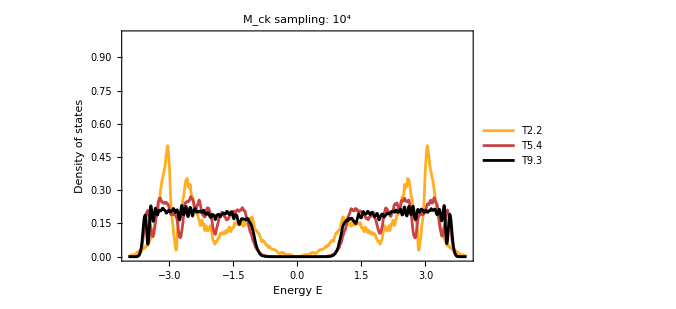

```mathematica
SmoothHistogram[evals,0.01,"PDF",
Frame->True,FrameLabel->{"Energy E","Density of states"},FrameStyle->Black,
ImageSize->500,ImagePadding->{{Automatic, 10}, {Automatic, 10}},LabelStyle->20,
PlotLabel->"M_ck sampling: 10^4",PlotRange->{0,1},PlotStyle->cLst]
```

## Visualize reflections and rotations (bonus):

The visualization toolbox of the HyperBloch package enables us to visualize how symmetries act on the graph representation of models. Let us see how generators of the triangle group and proper triangle group act on the fundamental Schwarz triangle.

### Fundamental Schwarz triangle:

We can highlighted individual Schwarz triangles in the Poincaré disk through the function  GetSchwarzTriangle. For example, let us extract the Polygon representing the fundamental Schwarz triangle associated with the identity element in the proper triangle group Δ^+(2,4,6):

```mathematica
sf=GetSchwarzTriangle[{2,4,6},"1"];
```

The fundamental Schwarz triangle can be visualized in the Poincaré disk, we may choose the function ShowTriangles to achieve this:

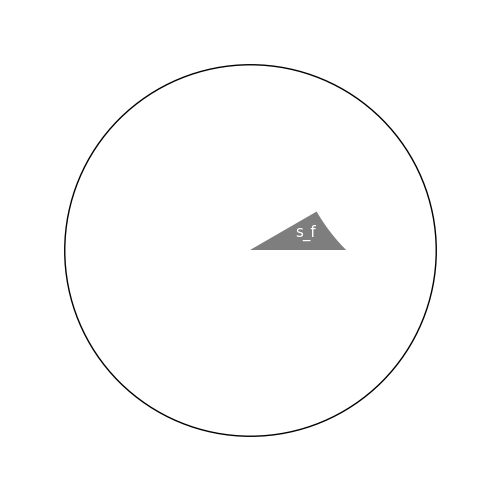

```mathematica
g1=Show[
ShowTriangles[{2,4,6},ImageSize->300,NumberOfGenerations->2],
Graphics[{Darker[Gray,0.01],sf}],
Graphics[{Text[Style["s_f",15,Thick,White],{0.3,0.09}]}],

ImageSize->500
]
```

### Reflections:

The reflections associated with the triangle group generators acting on the fundamental Schwarz triangle s_f can be indicated in the Poincaré disk through the function GetEdge which enables us to extract a Line representing the edge (or succession of edges) specified by vertices. We choose pairs of vertices such that each line extends a side of s_f shown as hyperbolic geodesics. Each vertex is of the form  {w_i,"g_i"}, where w_i specifies a  Wyckoff position and "g_i" a symmetry operation:

```mathematica
aLine=GetEdge[{2,4,6},{{1,"z^3*x"},{1,"z^3*x*z^3"}}];
bLine=GetEdge[{2,4,6},{{2,"x*y^2"},{2,"x*y^2*x"}}];
cLine=GetEdge[{2,4,6},{{3,"y^2"},{3,"y^2*z^3"}}];
```

The lines can be visualized in Poincaré disk together with the fundamental Schwarz triangle as follows:

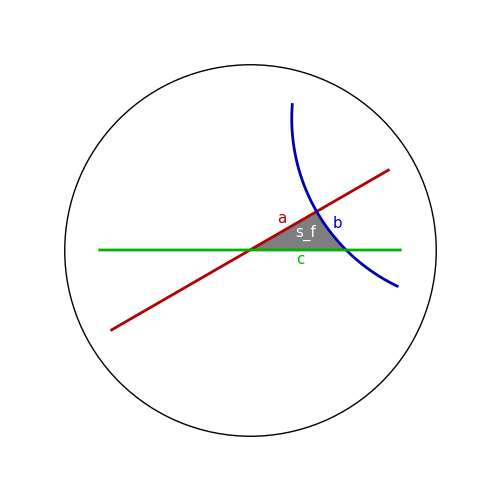

```mathematica
g2=Show[g1,

Graphics[{Darker[Red,0.3], AbsoluteThickness[2],aLine}],
Graphics[{Darker[Blue,0.3],AbsoluteThickness[2],bLine}],
Graphics[{Darker[Green,0.3],AbsoluteThickness[2],cLine}],

Graphics[{Darker[Red,0.3],Text[Style["a",15,Thick],{0.17,0.17}]}],
Graphics[{Darker[Blue,0.3],Text[Style["b",15,Thick],{0.47,0.14}]}],
Graphics[{Darker[Green,0.3],Text[Style["c",15,Thick],{0.27,-0.05}]}],

ImageSize->500
]
```

### Rotations:

Similarly, the rotations associated with the proper triangle group generators acting on the fundamental Schwarz triangle  s_f can be indicated in the Poincaré disk through the functions  GetSchwarzTriangle and GetVertex, the latter enables us to extract a Point representing a vertex in the Poincaré disk.
Under the right action of the proper triangle group generators the fundamental Schwarz triangle is transported as follows:

```mathematica
xsf=GetSchwarzTriangle[{2,4,6},"x"];
ysf=GetSchwarzTriangle[{2,4,6},"y"];
zsf=GetSchwarzTriangle[{2,4,6},"z"];
```

The Points representing the vertices of the fundamental Schwarz triangle, which are of the form {w_i,"g_i"}, can be extracted as follows:

```mathematica
x=GetVertex[{2,4,6},{1,"1"}];
y=GetVertex[{2,4,6},{2,"1"}];
z=GetVertex[{2,4,6},{3,"1"}];
```

In addition, let us indicate the rotations with segments of circles:

```mathematica
arcArrow[a_,r_,{start_,end_}]:=Module[{arrForm},
arrForm=Graphics[Line[{{{-1,1/2},{0,0},{-1,-1/2}}}]];
{Arrowheads[{{.005,1,arrForm}}],Arrow[Circle[a,r,{start,end}]]}]

xar=arcArrow[x[[1]],0.07,{3π/2-0.2,5π/2-0.5}];
yar=arcArrow[y[[1]],0.09,{π-0.3,3π/2-0.5}];
zar=arcArrow[z[[1]],0.11,{0.2,π/3+0.2}];
```

The vertices and Schwarz triangles can be visualized in Poincaré disk together with the fundamental Schwarz triangle as follows:

```mathematica
Show[g1,

Graphics[{Darker[Green,0.3],PointSize[0.02],x}],
Graphics[{Darker[Red,0.3],PointSize[0.02],y}],
Graphics[{Darker[Blue,0.3],PointSize[0.02],z}],

Graphics[{Darker[Green,0.4],AbsoluteThickness[1.5],xar}],
Graphics[{Darker[Red,0.4],AbsoluteThickness[1.5],yar}],
Graphics[{Darker[Blue,0.4],AbsoluteThickness[1.5],zar}],

Graphics[{Darker[Green,0.3],Opacity[0.4],xsf}],
Graphics[{Darker[Red,0.3],Opacity[0.4],ysf}],
Graphics[{Darker[Blue,0.3],Opacity[0.4],zsf}],

Graphics[{Darker[Green,0.5],Text[Style["x",15,Thick],{0.39,0.33}]}],
Graphics[{Darker[Red,0.5],Text[Style["y",15,Thick],{0.48,-0.16}]}],
Graphics[{Darker[Blue,0.5],Text[Style["z",15,Thick],{0.08,0.3}]}],

ImageSize->500

]
```

-Graphics-

Alternatively, we may as well use the function  ShowCellSchwarzTriangles together with the option TriangleRange and ShowTriangleLabels if the Schwarz triangles are within the unit cell specified by the (supercell) model graph, in order to indicate the Schwarz triangles, instead of the function GetSchwarzTriangle:

```mathematica
Show[g1,
ShowCellSchwarzTriangles[pcmodel,
ShowTriangleLabels->True,
TriangleLabelStyle->Directive[Black,Italic,18],
TriangleStyle->Lighter[Gray, 0.15],
TriangleRange->{1,2,7,12}],

Graphics[{Darker[Green,0.3],PointSize[0.02],x}],
Graphics[{Darker[Red,0.3],PointSize[0.02],y}],
Graphics[{Darker[Blue,0.2],PointSize[0.02],z}],

Graphics[{Darker[Green,0.4],AbsoluteThickness[3],xar}],
Graphics[{Darker[Red,0.4],AbsoluteThickness[3],yar}],
Graphics[{Darker[Blue,0.3],AbsoluteThickness[3],zar}],

Graphics[{Darker[Green,0.4],Text[Style["x",20,Thick],{0.48,0.20}]}],
Graphics[{Darker[Red,0.4],Text[Style["y",20,Thick],{0.38,-0.06}]}],
Graphics[{Darker[Blue,0.4],Text[Style["z",20,Thick],{0.12,0.12}]}],

ImageSize->500
]
```

-Graphics-

The triangles are labeled by the corresponding right action of the elements in T_Δ(Γ) acting on the fundamental Schwarz triangle s_f, written as words in terms of the generators x,y,z of the proper triangle group Δ^+. These labels are equivalent to the colored labels we have added manually.

```mathematica
NotebookSave[]
```